## Solution to Floquet test problem

Here we find a periodic solution to Duffing equation

x''+γ x'+w_0^2 x=-ϵ w_0^2(a(x/a))^3+w_0^2 F_0 sin(w t)

We first compute an approximate solution using perturbation theory. We'll use this as an initial guess in the Sundance code. The approximate solution is.

x_p(t)≈-0.75 cos(w t)+0.237sin(w t)

Next, we compute a periodic solution numerically and use it as the base of a Floquet analysis. The Floquet eigenvalue is

λ≈0.1231

```mathematica
x[t_]=(A0 +ϵ A1) Sin[w t] + (B0 + ϵ B1) Cos[w t] + ϵ A3 Sin[3 w t]+ ϵ B3 Cos[3 w t]
```

(B0+B1 ϵ) cos(t w)+B3 ϵ cos(3 t w)+(A0+A1 ϵ) sin(t w)+A3 ϵ sin(3 t w)

```mathematica
R = TrigReduce[Expand[x''[t] + w0^2 x[t] + γ x'[t] + ϵ w0^2 /a^2 x[t]^3 - F w0^2 Sin[w t]]];
```

```mathematica
R1 = Normal[Series[R,{ϵ,0,1}]]
```

-B0 cos(t w) w^2-A0 sin(t w) w^2+A0 γ cos(t w) w-B0 γ sin(t w) w+B0 w0^2 cos(t w)+A0 w0^2 sin(t w)-F w0^2 sin(t w)+ϵ ((3 w0^2 sin(t w) A0^3)/(4 a^2)-(w0^2 sin(3 t w) A0^3)/(4 a^2)+(3 B0 w0^2 cos(t w) A0^2)/(4 a^2)-(3 B0 w0^2 cos(3 t w) A0^2)/(4 a^2)+(3 B0^2 w0^2 sin(t w) A0)/(4 a^2)+(3 B0^2 w0^2 sin(3 t w) A0)/(4 a^2)-B1 w^2 cos(t w)+(3 B0^3 w0^2 cos(t w))/(4 a^2)+B1 w0^2 cos(t w)+A1 w γ cos(t w)-9 B3 w^2 cos(3 t w)+(B0^3 w0^2 cos(3 t w))/(4 a^2)+B3 w0^2 cos(3 t w)+3 A3 w γ cos(3 t w)-A1 w^2 sin(t w)+A1 w0^2 sin(t w)-B1 w γ sin(t w)-9 A3 w^2 sin(3 t w)+A3 w0^2 sin(3 t w)-3 B3 w γ sin(3 t w))

```mathematica
c1 = Integrate[R1 Cos[w t], {t, 0, 2 Pi/w}]
```

1/(4 a^2 w)π (4 (-B1 ϵ w^2+A0 γ w+A1 γ ϵ w+B0 (w0^2-w^2)+B1 w0^2 ϵ) a^2+3 B0 (A0^2+B0^2) w0^2 ϵ)

```mathematica
s1 = Integrate[R1 Sin[w t], {t, 0, 2 Pi/w}]
```

1/(4 a^2 w)π (3 A0 (A0^2+B0^2) w0^2 ϵ-4 a^2 (A1 ϵ w^2+B0 γ w+B1 γ ϵ w+F w0^2+A0 (w^2-w0^2)-A1 w0^2 ϵ))

```mathematica
c3 = Integrate[R1 Cos[3w t], {t, 0, 2 Pi/w}]
```

(π (4 (B3 (w0^2-9 w^2)+3 A3 w γ) a^2+B0 (B0^2-3 A0^2) w0^2) ϵ)/(4 a^2 w)

```mathematica
s3 =Integrate[R1 Sin[3w t], {t, 0, 2 Pi/w}]
```

-(π (4 (9 A3 w^2+3 B3 γ w-A3 w0^2) a^2+A0 (A0^2-3 B0^2) w0^2) ϵ)/(4 a^2 w)

```mathematica
ab0 = Solve[{c1==0,s1==0}/. ϵ->0 ,{A0,B0}]
```

{{A0→(F w0^2 (w0^2-w^2))/(w^4-2 w0^2 w^2+γ^2 w^2+w0^4),B0→-(F w w0^2 γ)/(w^4-2 w0^2 w^2+γ^2 w^2+w0^4)}}

```mathematica
ab1 =FullSimplify[Solve[{c1==0,s1==0} ,{A1,B1}]/. ab0[[1]]]
```

{{A1→-(3 F^3 w0^8 (w^4-(2 w0^2+γ^2) w^2+w0^4))/(4 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3),B1→(3 F^3 w w0^8 (w0^2-w^2) γ)/(2 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3)}}

```mathematica
ab3 = FullSimplify[Solve[{c3==0,s3==0},{A3,B3}]/. Flatten[{ab0,ab1}]]
```

{{A3→(F^3 w0^8 (3 w^4 γ^4-12 w^2 (3 w^4-4 w0^2 w^2+w0^4) γ^2+(w0^2-9 w^2) (w0^2-w^2)^3))/(4 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3 ((w0^2-9 w^2)^2+9 w^2 γ^2)),B3→(F^3 w w0^8 γ (3 (5 w^2-w0^2) (w^2-w0^2)^2+w^2 (5 w0^2-9 w^2) γ^2))/(2 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3 ((w0^2-9 w^2)^2+9 w^2 γ^2))}}

```mathematica
coeffs = Flatten[{ab0, ab1, ab3}]
```

{A0→(F w0^2 (w0^2-w^2))/(w^4-2 w0^2 w^2+γ^2 w^2+w0^4),B0→-(F w w0^2 γ)/(w^4-2 w0^2 w^2+γ^2 w^2+w0^4),A1→-(3 F^3 w0^8 (w^4-(2 w0^2+γ^2) w^2+w0^4))/(4 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3),B1→(3 F^3 w w0^8 (w0^2-w^2) γ)/(2 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3),A3→(F^3 w0^8 (3 w^4 γ^4-12 w^2 (3 w^4-4 w0^2 w^2+w0^4) γ^2+(w0^2-9 w^2) (w0^2-w^2)^3))/(4 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3 ((w0^2-9 w^2)^2+9 w^2 γ^2)),B3→(F^3 w w0^8 γ (3 (5 w^2-w0^2) (w^2-w0^2)^2+w^2 (5 w0^2-9 w^2) γ^2))/(2 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3 ((w0^2-9 w^2)^2+9 w^2 γ^2))}

```mathematica
vals = {F->1/2, γ->2/3,a->1,w-> 1, w0->1, ϵ->1/2}
```

{F→1/2,γ→2/3,a→1,w→1,w0→1,ϵ→1/2}

```mathematica
coeffs //. vals
```

{A0→0,B0→-3/4,A1→243/512,B1→0,A3→27/8704,B3→-27/2176}

```mathematica
f0 = {A0, B0} /. (coeffs //. vals)
```

{0,-3/4}

```mathematica
f1 = {A1, B1} /. (coeffs //. vals)
```

{243/512,0}

```mathematica
f3 = {A3, B3} /. (coeffs //. vals)
```

{27/8704,-27/2176}

```mathematica
soln = Join[coeffs, vals]
```

{A0→(F w0^2 (w0^2-w^2))/(w^4-2 w0^2 w^2+γ^2 w^2+w0^4),B0→-(F w w0^2 γ)/(w^4-2 w0^2 w^2+γ^2 w^2+w0^4),A1→-(3 F^3 w0^8 (w^4-(2 w0^2+γ^2) w^2+w0^4))/(4 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3),B1→(3 F^3 w w0^8 (w0^2-w^2) γ)/(2 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3),A3→(F^3 w0^8 (3 w^4 γ^4-12 w^2 (3 w^4-4 w0^2 w^2+w0^4) γ^2+(w0^2-9 w^2) (w0^2-w^2)^3))/(4 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3 ((w0^2-9 w^2)^2+9 w^2 γ^2)),B3→(F^3 w w0^8 γ (3 (5 w^2-w0^2) (w^2-w0^2)^2+w^2 (5 w0^2-9 w^2) γ^2))/(2 a^2 ((w^2-w0^2)^2+w^2 γ^2)^3 ((w0^2-9 w^2)^2+9 w^2 γ^2)),F→1/2,γ→2/3,a→1,w→1,w0→1,ϵ→1/2}

```mathematica
y[t_] = x[t] //. soln //N
```

-0.75 cos(t)-0.00620404 cos(3. t)+0.237305 sin(t)+0.00155101 sin(3. t)

```mathematica
y'[t]//N
```

0.237305 cos(t)+0.00465303 cos(3. t)+0.75 sin(t)+0.0186121 sin(3. t)

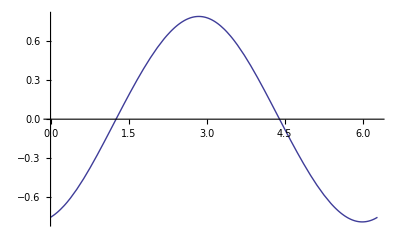

```mathematica
Plot[y[t],{t,0,2 Pi}]
```

```mathematica
y[0]
```

-3291/4352

```mathematica
y'[0]
```

1053/4352

```mathematica
e[u_]:= D[u,{t,2}]+ γ D[u,t]+w0^2 u+ϵ w0^2 /a^2 u^3 - F w0^2 Sin[w t]==0
```

```mathematica
Map[Coefficient[#,δ]&,Expand[e[up[t]+ δ du[t]]]]/. soln
```

3/2 du(t) (up(t))^2+du(t)+(2 du'(t))/3+du''(t)==0

```mathematica
bvp = {e[u[t]], u[0]==u[2Pi],u'[0]==u'[2Pi]}/. soln
```

{(u(t))^3/2+u(t)-(sin(t))/2+(2 u'(t))/3+u''(t)==0,u(0)==u(2 π),u'(0)==u'(2 π)}

```mathematica
nSoln = NDSolve[bvp,u[t],{t,0,2Pi}][[1]]
```

{u(t)→InterpolatingFunction[(0. | 6.28319),<>][t]}

```mathematica
up[t_] = u[t]/. nSoln
```

InterpolatingFunction[(0. | 6.28319),<>][t]

```mathematica
de = Map[Coefficient[#,δ]&,Expand[e[up[t]+ δ du[t]]]]/. soln
```

3/2 du(t) (InterpolatingFunction[(0. | 6.28319),<>][t])^2+du(t)+(2 du'(t))/3+du''(t)==0

```mathematica
soln1 = NDSolve[{de,du[0]==1,du'[0]==0},du[t],{t,0,2Pi}]
```

{{du(t)→InterpolatingFunction[(0. | 6.28319),<>][t]}}

```mathematica
soln2 = NDSolve[{de,du[0]==0,du'[0]==1},du[t],{t,0,2Pi}]
```

{{du(t)→InterpolatingFunction[(0. | 6.28319),<>][t]}}

```mathematica
z[t_]=du[t]/. soln2[[1]]
```

InterpolatingFunction[(0. | 6.28319),<>][t]

```mathematica
z'[t]
```

InterpolatingFunction[(0. | 6.28319),<>][t]

```mathematica
D[du[t]/. soln1[[1]],t]
```

InterpolatingFunction[(0. | 6.28319),<>][t]

```mathematica
du1[t_]=du[t]/. soln1[[1]]
```

InterpolatingFunction[(0. | 6.28319),<>][t]

```mathematica
du2[t_]=du[t]/. soln2[[1]]
```

InterpolatingFunction[(0. | 6.28319),<>][t]

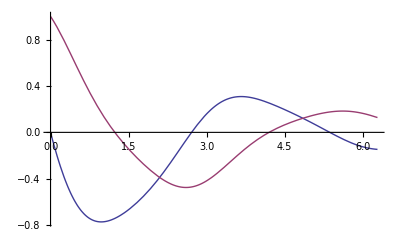

```mathematica
Plot[{du1'[t],du2'[t]},{t,0,2Pi}]
```

```mathematica
K = {{du1[2Pi],du2[2Pi]},{du1'[2Pi],du2'[2Pi]}}
```

(0.0764999 | 0.036701
-0.146705 | 0.127849)

```mathematica
Abs[Eigenvalues[K]]
```

{0.123145,0.123145}

```mathematica
ClearAll[v]
```

```mathematica
v[t_] = u[t] /. nSoln
```

InterpolatingFunction[(0. | 6.28319),<>][t]

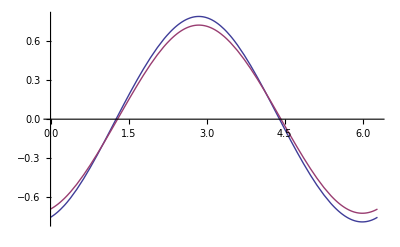

```mathematica
Plot[{y[t],v[t]},{t,0,2Pi}]
```

```mathematica
y[t]
```

-(3 cos(t))/4-(27 cos(3 t))/4352+(243 sin(t))/1024+(27 sin(3 t))/17408